## Paper #3 Model of An Approaching Meteor

The model simulates the event of a metallic (iron core) meteor approaching the Earth from outer space at some distance away from  Earth, passing through the vacuum of space, Earth’s atmosphere, and finally its collision with Earth’s surface as it is attracted by the force of gravity. The iron core makes sure that the meteor will not completely deteriorate in its entry to the atmosphere while undergoes the force of atmospheric drag. This model is encapsulated by four major equations detailing the position of the meteor, the drag of the meteor, the mass of the meteor, and the density of air. This model takes specific care into simulating the effects of drag in the atmosphere which deteriorates the mass of the meteor, thus changing its descent towards the Earth’s surface and the force of gravity it experiences. 

-Graphics-

## Introduction

1. The density of air
	This equation plays a small but critical role in the overall modeling of the meteor. When an object is in vacuum of space it does not undergo the force of drag due to the lack of air. In turn, this means the object does not experience the force of air friction. Moreover, the meteor will not combust or deteriorate in anyway, thus it won’t lose any mass. However, as the object enters Earth’s atmosphere, the density of air rapidly increases causing both the change in mass and drag of the meteor to “turn on” or “activate” suddenly. The drag function is based on the parameter φ  which is the density of air at the current distance from earth. The density of air is a function of the position (s).  In space φ is zero, because there is no air to make an atmosphere. However, once the position drops below 96560 meters the meteor begins to enter the atmosphere (of Earth) where air acts as a dampening force slowing the descent of the meteor and causing an increase in temperature and friction to cause the rapid destruction of the meteor. X is the parameter which is the air density in a given section of the planet the meteor is entering. The only initial condition that is necessary for a solution is the starting position of the meteor; essentially, is the meteor in the atmosphere, or is it outside of the atmosphere.

### Equation Density of Air: φ = Piecewise[{{0, if S>96560}, {x, if S≤ 96560}}]

2. The drag of the meteor
	This equations is a large chunk in contributing to the change in position equation for the meteor. As the object falls into earth’s atmosphere, air friction in the form of drag acts as a dampening force against it. Drag depends on many things, such as the the overall resistance (Cd) caused by the shape of the object, the air density of the atmosphere (φ), and the surface area of the object (A). As the object begins to move faster, it will experience higher amounts of resistance because it essentially pushes harder against the atmosphere causing the force of drag to push back proportionally as hard. D_1 is a function of the surface area of the object (A) which will be determined by approximating its area by using the meteor’s mass. Meteors come in all shapes and different sizes; however, they can be average to a spherical shape. Because of this assumption, the mass of the meteor can be used to approximate the surface area of a sphere as the radius, meaning (A) depends on the mass of the meteor. The drag of the meteor is equal to the drag coefficient of the object (overall resistance) multiplied by the air density and reference area. The only initial condition necessary is the mass of the meteor and the value of φ to determine if the meteor is actually in the atmosphere to experience drag.

### Equation Drag of the Meteor: D_1= 1/2*Cd*φ*A

3. The change in mass of the meteor
	As the meteor enters the atmosphere it will begin to combust due to the air friction which will quickly begin to deteriorate its mass; however, we assume the meteor has a metallic core meaning this process will not result in the meteor being completely deteriorated under normal conditions. This will depend on a constant of proportionality (β) between the change in mass of the meteor and its drag, the drag of the meteor (D_1), and the objects velocity squared. The proportionality parameter (β) is referred to as the burning coefficient as it relates to the relative composition of the meteor between how rocky and metallic it is; a higher composition of metal means the meteor is more sturdy and will not deteriorate as fast in the atmosphere resulting in a lower value of (β). As the object begins to move faster, it  will experience higher amounts of resistance which lead to a greater amount of deterioration. One big assumption regarding the deterioration of the meteor is that the process occurs uniformly like a shell being removed layer by layer which keeps the change in surface area of the meteor relatively linear, compared with if the meteor was to split into chunks which would greatly increase the surface area relative to the mass. The dependent variable is the mass of the meteor (m). The independent variable is the time (t) since the first observance of the meteor. Velocity is the first derivative of position and in the definition of drag velocity it is squared to represent that air resistance is not directly proportional to speed, this is due to the compression of air when increasing velocity; however, this process removes the sign of the velocity, and thus its direction. In other words velocity squared which can be considered (s')^2 is rewritten as |s’|s’ to preserve the direction of the meteor and make drag the opposite force of the velocity. The initial conditions necessary to solve is the value of position (s), velocity (s’), and the mass of the meteor (m). The position will determine if drag D_1 exists and the initial velocity determines the speed at which the meteor could potentially be losing mass by deterioration in the atmosphere. Obviously, the initial mass determines at what rate the meteor will proportionally lose mass. Note that this function only exists when φ is greater than zero.

### Equation Change in Mass of the Meteor: ⅆm/ⅆt=-β*m*D_1*|S'|*S'

4. The change in position of the meteor 
	This equation draws heavily upon Newtons 2nd law, “the force F is the product of an object’s mass and its acceleration: F=M*A.” The biggest driving factor of this model is a meteor approaching Earth is obviously going to be affected by the gravitational pull of the planet. Additionally, when falling in the atmosphere this meteor will experience drag do to atmospheric friction. These three ideas together are related  because acceleration is the second derivative of position (s’’). This means it is simple to express the position of the meteor in terms of the forces it undergoes, such as gravity from earth and its drag in the atmosphere. The force that the meteor experiences if equal to force of gravity which pulls the meteor into the Earth minus the force of drag which pushes against the meteor as it falls. The gravitational force is also based on Newton’s law of universal gravitation F=G(m_1 m_2)/r^2. It explains the relationship between the attractive force of two objects, their masses, and the distance between them. The gravitational constant (g) is the value observed to relate the mass (m_1) of one object to another (m_2) based on the distance between them (r^2). The dependent variable
is the position of the meteor from the surface of the Earth plus the radius of the Earth, we assume the radius of the meteor is negligible relative to its position away from the Earth and the Earth’s radius. Another assumption regards that the meteor approaches the Surface of the Earth perpendicular to the surface instead of at an angle; thus, we can ignore using trigonometric functions to represent the angle at which the meteor approaches the planet in order to simplify the model. The independent variable is the time (t) since the first observance of the meteor. On the left side of the equation is the net forces experienced by the meteor. On the right is the modified gravitational equation which used the gravitational constant (g), the mass of the meteor (m), and the mass of the planet Earth (M). The distance between those two objects is radius of the Earth plus the distance to the meteor (s+r). Also included is the force of drag resisting the descent of the meteor into Earth. The initial conditions needed to solve for an unique solution are the initial values of  velocity (s’),  position (s), and the mass of the meteor (m). Combining these all together you are able to find if drag exists, how fast the meteor is approaching Earth, and how much force gravity exerts onto the meteor.

### Equation Change in Position of the Meteor: m* (ⅆ^2 S)/(ⅆ t^2)=-g(M*m)/(S+r)^2-D_1*|S'|*S’

## Table of Variable Units

Variables  | Name  | Units 
t | Time  | seconds (sec)
s | Distance from surface of the Earth | meters (m)
m | Mass of Meteor | kilograms (kg)

## Parameters

1. The density of air in Earth’s Atmosphere
This equation has only one parameter which is the density of air (x) at the given location of the falling meteor which can vary given atmospheric conditions, such as temperature, pressure, height, temperature lapse rate, and many other factors. This value is useful in the density of air equation because it determines how much air is in a given volume. Given a higher amount of air density, there are more molecules of “air” which must be fought against by an object moving through it. It is best to think of air like molasses which hinders movement. Air is the medium of movement when in the atmosphere, which dampens, slows, and causes the meteor to deteriorate because of its friction: drag. A higher value of the density of air will causes the meteor to experience more drag, therefore slowing its velocity and increasing deceleration; also, this causes the meteor to break apart at a faster rate. A lower value of the density of air does the complete opposite. The initial value of the position (s) is the key factor in determining the air density, if any. If the position of the meteor is above 96,560 meters, it is the vacuum of space.

2. The drag of the meteor 
This equation has one parameters the drag coefficient (Cd) and the surface area of the meteor (A). The drag coefficient is a unitless quantity meant to quantify an object’s base flow and aerodynamics of the object. An object that is more resistance and hinders the flow of air around itself has a higher drag coefficient compared to an object which more easily allows air to move around it (or through it). The value usually ranges between zero and one. A value of zero indicates a given shape causes no disturbance to the flow of the medium it is in (air or water). A higher value represents a higher amount of resistance by the object. For example, the Eiffel Tower has a drag coefficient between 1.8-2 and the Empire State Building is between 1.3-1.5. For a somewhat spherical object like a meteor, it can range between .4-1 depending on its exact body shape
(https://web.archive.org/web/20070715171817/http://aerodyn.org/Drag/tables.html). The larger the drag coefficient the more drag the object will experience. This will cause a larger amount of deterioration in the mass and deceleration of the object. The reference area is the specific part of an object that is experience the flow of the medium. This could be the portion of a boat that is in the water or the underbelly of a parachute falling. For an object like a meteor the reference area depends on its side which is facing the earth as it falls. It can be roughly approximated by the size of its mass. A meteor with more mass (assuming the same composition compared to a meteor of lesser mass) will have a larger size (considering a metallic-core meteor class), therefor it will have a larger surface area to experience the force of drag. In turn, the force of drag will deteriorate the surface area as the meteor combusts in the atmosphere from the force of atmospheric friction. This works as a feedback loop: first decreasing the force of drag, then decreasing the the change in the surface area. The initial value of the mass determines the severity of the drag value. If the mass of the meteor is larger, it will have a greater reference area. Given this, the speed of the meteor will slow (if in the atmosphere) and the mass will deteriorate faster because there is more exposed area to the force of drag.

3. The change in mass of the meteor 
This equation has one parameter the burning coefficient of the meteor (β). It is a proportionality depending on the exact composition of the meteor. Meteors in space greatly vary in their exact composition. From stony meteorites containing rocks and silicates to stony-iron meteorites with iron and nickel. Meteors without a metallic core will completely combust in Earth’s atmosphere before ever reaching the surface; however, those with higher amounts of iron and nickel will survive. The burning coefficient of the meteor depends on the amount of stony and rocky materials in the meteor. A higher amount of these rocky composites leads to a greater value of the burning coefficient which in turn leads to the meteor deteriorating faster. A meteor composed entirely of metal (incredibly rare) will have a lower value of the burning coefficient, thus experience less deterioration in the atmosphere. The initial condition required is the mass of the meteor. A higher mass will influence the rate at which the meteor deteriorates: a higher mass meteor will burn faster in atmosphere, compared to a lower mass meteor of the same burning coefficient.

4. The change in position of the meteor 
This equation has three parameters: the gravitational constant, the mass of the planet, and the radius constant of the planet. The gravitation constant is a proportionality in Newton’s Law of Universal Gravitation used to related the force of gravity and the mass’s of the objects and their distance between them. The mass of the planet is simply the mass of the Earth. The radius of the planet is simply the radius of the earth. All of these values are used in the gravity section of the meteor’s position.

## Table of Parameter

Parameters and Constants | Name | Units
g | Graviational constant
	(6.67430*10^-11) | newton meter squared per kilogram squared
						((N*m^2)/kg^2)
M | Mass of the Earth
	(5.972*10^24) | kilograms
     (kg)
r | radius of Earth
	(6.371*10^6) | meters 
   (m)
x | Density of Air | kilogramgs per meter cubed 
				(kg/m^3)
Cd | Drag Coefficient  | unitless
β | Burning coefficient of meteor  |  second per meter kilogram 
			  (sec/(m*kg))
A | reference area of the meteor  
     (roughly equal to m^(2/3)) | meter squared 
	   (m^2)
φ | Air density at location | kilograms/meter^3
	   (kg/m^3)
D_1 | Drag Value | kilogram/meter 
	  (kg/m)

## Non-dimensionalization

There are three variables that need to be replaced with non-dimensional variables: the position of the meteor (s), the mass of the meteor (m), and the time (t). The drag value does not need to be replaced because it can be substituted into the other equations when needed. And the air density is a function of the position; however, it will still need to be non-dimensionalized to give meaning to its piecewise function. Let  k be the non-dimensional variable for position of the meteor (s), j be the non-dimensional variable for the mass of meteor (m), p be the non-dimensional variable for the air density (φ), and τ be the non-dimensional variable for time (t).

Scaling factors are composed of parameters already used in the equations. The purpose of non-denationalization is to remove the physical dimensions and physical quantities, such as units by substitutions of non-dimensional variables paired with scaling factors. The parameters are meant to cancel out and drop out the units for the new equations. Therefore, by combination of select parameters with the original variables, unit-less equations can be created.

Non-dimensional Variable              | Variable replacing  |             Scaling with parameters
k | s | k=(1/r)s
j | m | j=(1/M)m
p | φ | p=(1/x)φ
τ | t | τ=(1/βMr)t

These equations and their derivatives can then be substituted in the original equations like change of position and mass of the meteor in order to measure the effects of the parameters. 

Non-dimensional equation | Derivate of non-dimensional equation | Double Derivative of non-dimensional equation 
k=(1/r)s | ⅆk=(1/r)ⅆs | ⅆ^2 k=(1/r)ⅆ^2 s
j=(1/M)m | ⅆj=(1/M)ⅆm | □
p=(1/x)φ | □ | □
τ=(1/βMr)t | ⅆτ=(1/βMr)ⅆt | ⅆ τ^2=(1/βMr)^2 ⅆ t^2

The equations can be substituted into the original to create the new non-dimensionalization equations. 
For the air density this is relatively simply because it is only one substitution. Depending on the value of “k”, “p” will either be zero or one. 

Original Equation  | φ=Piecewise[{{0, if S>96560}, {x, if S≤ 96560}}]
Substitution | (xp)=Piecewise[{{0, if (rk)>96560}, {x, if (rk)≤ 96560}}]
Simplification | xp=Piecewise[{{0, if rk>96560}, {x, if rk≤ 96560}}]

For the change in mass of the meteor. 

Original Equation | ⅆm/ⅆt=-β*m*D_1*|S'|*S'
Substitution  | (ⅆj/ⅆτ*1/rβ)=-β*(j*M)*(1/2*Cd*(x*p)*A)*|(ⅆk/ⅆτ*1/Mβ)|*(ⅆk/ⅆτ*1/Mβ)
Simplification | ⅆj/ⅆτ=((-r*x*A)/M)*(1/2 j*Cd*p)*|ⅆk/ⅆτ|*ⅆk/ⅆτ

For the change in position of the meteor.

Original Equation | m* (ⅆ^2 S)/(ⅆ t^2)=-g(M*m)/(S+r)^2-D_1*|S'|*S'
Substitution | (M*j)* ((ⅆ^2 K)/(ⅆ τ^2)*1/(M^2*r*β^2))=-g(M*(M*j))/((r*K)+r)^2-(1/2*Cd*(x*p)*A)*|ⅆk/ⅆτ*1/Mβ|*ⅆk/ⅆτ*1/Mβ
Simplification | (ⅆ^2 K)/(ⅆ τ^2)=((M^3*β^2*g)/r)*(1/(1+K)^2)-(1/2*Cd*p)/j*|ⅆk/ⅆτ|*ⅆK/ⅆτ


For the non-dimensionalized equation of the change in mass of the meteor the parameters of the radius of the planet, air density, surface area, mass of planet, and drag coefficient are used to give meaning. First off the radius of the planet greatly affects the deterioration of the meteor because with a longer radius the Meteor will experience a lower force of gravity from Earth meaning the net force on the meteor will lean more towards the force of atmospheric drag causing the meteor to deteriorate more. The air density of the atmosphere relates to the amount of molecules in a space, if more are present the meteor will have more “collisions” to fight against. Hence, a higher density will cause the meteor to experience higher amounts of atmospheric friction and deteriorate more rapidly. The surface area of the meteor determines the size of the meteor which undergoes the force of atmospheric drag, related to the density of the atmosphere, the more collisions there are with molecules from the atmosphere, then the more deterioration will occur as a result of the increased force of drag. The larger the mass of the planet, the lower the deterioration of the meteor. This is because the force of gravity increases when the mass of the two relative objects increase resulting in a lower net force on the meteor when in the atmosphere. A higher value of the drag coefficient means a larger deterioration of the meteor. The drag coefficient relates to the flow of air flowing around the meteor, if the meteor hinders move air from flowing around it leading to an increase in the drag coefficient it will experience higher amounts of atmospheric drag causing the meteor to be destroyed more rapidly.

For the non-dimensionalized equation of the change in position of the meteor the parameters of the mass of the planet, the burning coefficient, the gravity constant, the radius of the planet, and the drag coefficient are used to give meaning. Starting with the mass of the planet, if the planet is larger there will be a higher force of attraction between Earth and the meteor. Hence, the meteor will accelerated faster towards earth decreasing the position of the meteor to Earth. The burning coefficient is based on the composition of the meteor regarding its rocky and metallic components, with more rocky components the value of β will be greater causing the deterioration of the meteor to be greater from the force of atmospheric drag. Because the meteor is more rapidly becoming smaller it will undergo a relatively less force of atmospheric drag compared to the force gravity causing it further decrease the position of the meteor to Earth. The gravity constant obviously affects the proportion at which the meteor experiences the force of gravity, with a higher value of g the meteor will be more attracted to the planet causing it to fall faster to the surface of the Earth increasing the change in the position of the meteor towards Earth. The radius of the planet relates to the force of gravity because with a higher distance between the Earth and the meteor the effects of gravity will be weakened, causing the net force on the meteor to decrease leading to a lower change in position of the meteor towards Earth. Finally the drag coefficient affects the force of drag, increasing the amount of drag the meteor experiences causing the force of atmospheric drag to mutually increase hindering the approach of the meteor to Earth; thus, the change in position of the meteor will decrease as the meteor slows due to the resistance of the atmosphere.

## Analytical Solutions

## Sample Graph Under Normal Conditions

The two differential equations are not simple enough to be solved for an analytical solution so only numerical values can be used. The differential equations of the position of the meteor and mass of the meteor depend on each other which makes it difficult to untangle their effects on each other. Conversely however, when graphs are used it is easy to observe their mutual effects. One basic premise for the model is that the meteor will be attracted to the Earth by its gravitational pull, causing it to accelerate towards the surface of the earth; however, because of the effects of the atmosphere, namely the force of air resistance, the meteor’s descent to the surface will be disturbed as it deteriorates from this dampening force of friction. So as the position decreases (in the atmosphere), the mass will dramatically decrease, resulting in a lower attractive gravitational force which slows the meteors descent, but because the distance to the earth is decreasing at the same time, the attractive gravitational force will also go up.

Assume for all other graphs when no other parameter is changed that these values are being used. 

Paramter | Value
g |  6.67430*10^-11
M | 5.972*10^24
r |  6.371*10^6
φ | 1.225
Cd | .6
β |  5*10^-14
m0 |  5*10^10
s[0] | 600000
s'[0] | 0

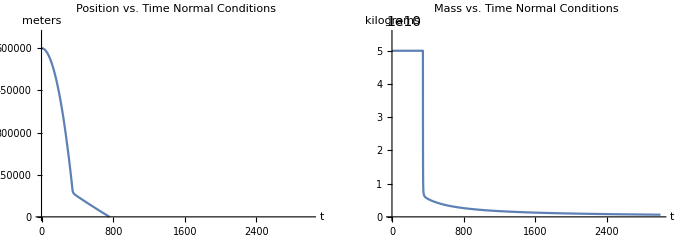

{Impact time with surface,{t→759.553}}

{Resulting Meteor Size,2.77897×10^9}

{Percent of Original Meteor,5.55794 %}

These graphs show the basic relationship between the two differential equations of the position and mass. Note that the mass remains static until the position of the meteor drops below the atmosphere, which causes a sudden change in the velocity and acceleration of the meteor. These changes are seen in the graph of position vs. time as the slope of the position changes in the atmosphere to become less steep and its downwards concavity becomes more flat signalling respectively the slowing of velocity and acceleration. While at the same time, the mass rapidly decreases. The decrease is caused by atmospheric drag deteriorating the meteor proportional to its surface area. 
Also observe that after roughly 760 seconds of travel time to the surface of the Earth that the meteor only retained 5.5% of its original mass meaning a substantial amount had burned away due to the atmospheric friction. The sudden corner in the graph of position occurs when the meteor enters the atmosphere and drag begins to influence the meteors velocity towards the Earth. Likewise on the graph of the mass, it remains constant until the time at which the meteor enters the Earth’s atmosphere resulting in the sudden dip. This sudden corner on the mass vs. time graph is quickly alleviated when the mass becomes too small (and thus its surface area) relative to its speed which the force of atmospheric friction is acting upon.

## Graphs changing Air Density in Atmosphere

Air density is a major factor in calculating the atmospheric friction the meteor will experience. Just in thought, the more dense the air is the more particles that will be in a give space of the atmosphere. Each one of these particles in turn will causing a dampening friction force towards the incoming meteor; however, its effects will only be seen when the meteor drops below the atmosphere. This means that all graphs with varying air density will look exactly the same pre-atmosphere. But graphs with increased friction from higher air densities means the mass will decrease at a faster rate. Ultimately it comes down to whether the dampening force given the increase in air density will be greater than the attractive gravity force of the rapidly shrinking meteor.

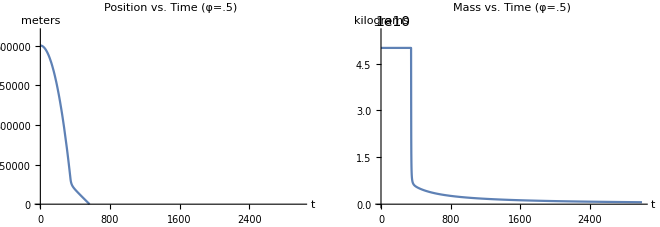

{Impact time,{t→565.455}}

{Resulting Meteor Size,3.85303×10^9}

{Percent of Original Meteor,7.70607 %}

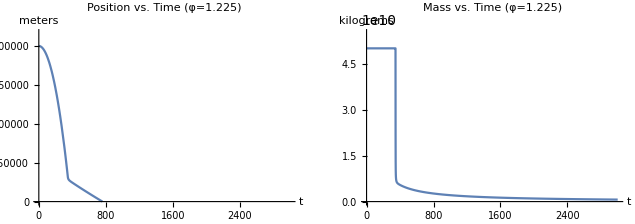

{Impact time,{t→759.553}}

{Resulting Meteor Size,2.77897×10^9}

{Percent of Original Meteor,5.55794 %}

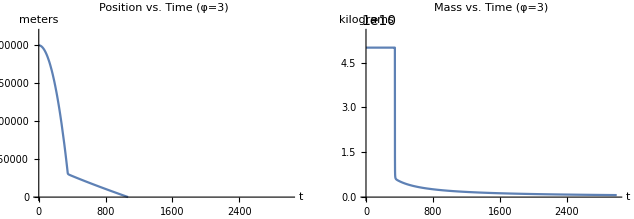

{Impact time,{t→1068.63}}

{Resulting Meteor Size,1.94839×10^9}

{Percent of Original Meteor,3.89679 %}

Observe that as the air density increases in the atmosphere, the mass of the meteor decreases much more rapidly resulting in a lower percent mass at the impact time (time from t=0 until the meteor hits the surface) and the impact time increases. The increase in time until impact is caused by the fact that with the decreased mass there is a lower gravitational force pulling the meteor down. In addition, the air density provides a greater force of drag which slows the descent of the meteor. As a result the change in air density not only influences the drag, but it also influences the mass of the meteor—the deterioration from the atmospheric drag when the meteor enters the atmosphere will proportionally break up the meteor—which acts as a feedback loop causing the force of drag to be much greater than the attractive gravitational force. The rate of disintegration (negative change in mass) is so huge before slowing because the meteor’s surface area and velocity decrease to such an amount that the atmospheric drag causes less damage to the meteor. Looking at the equation for the change in mass,  only the mass, surface area, and velocity are changing; as time goes on after the meteor has entered the atmosphere because of the force of atmospheric drag the mass and therefore the surface area will decrease because of deterioration. Also, the velocity will decrease from the drag pushing against the meteor. With all three of the parameters decreasing, it causes the deterioration to also slow after its initial drop from the original mass and velocity when the meteor entered the atmosphere. One could imagine this situation extends to atmospheres beyond gaseous like Earth’s atmosphere. If the medium the meteor traveled through was more “thick” and therefore dense it would take an increasingly longer time to fall through it, but if its too “thick” the meteor will not have very much velocity to experience drag. Note, as the density of air increased six-fold, the impact time roughly doubled while the percent of the original mass was halved.

## Graphs changing Burning Coefficient

The burning coefficient (β) is a proportionality parameter relating the rate of the mass of the meteor and the force of drag. The composition of a more metallic meteor will decrease the burning coefficient because the meteor is resilient and won’t deteriorate as much in the atmosphere. A more rocky meteor will have a greater value of the burning coefficient because it will undergo more damage as a result from the force of atmospheric drag. This parameter only has meaning when the meteor is in the atmosphere because the force of atmospheric drag can not occur without air (or any other particles). As the burning coefficient increases, the meteor will “burn” more, and as burning coefficient decreases, the meteor will “burn” less. Changes to the burning coefficient influence the change in the mass of the meteor as it falls through the atmosphere. Moreover, because the force of gravity is proportional to the mass of meteor and the force of drag is proportional to the surface area of the meteor which is closely related to its mass (m^(2/3)), then the meteor that deteriorates more (higher β value) will also experience a lower force of gravity.

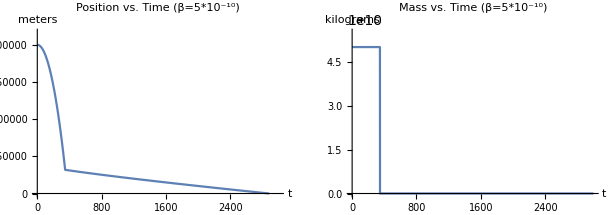

{Impact time with surface,{t→2883.24}}

{Resulting Meteor Size,72685.7}

{Percent of Original Meteor,0.000145371 %}

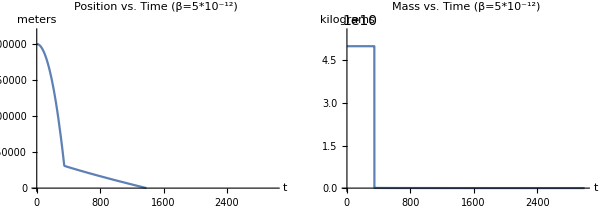

{Impact time with surface,{t→1384.67}}

{Resulting Meteor Size,1.54279×10^7}

{Percent of Original Meteor,0.0308557 %}

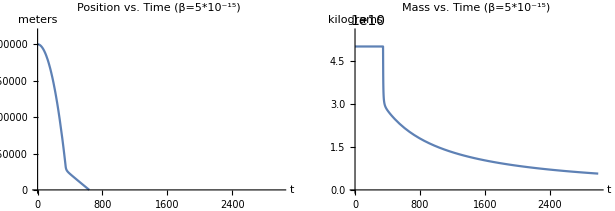

{Impact time with surface,{t→637.289}}

{Resulting Meteor Size,2.09755×10^10}

{Percent of Original Meteor,41.9511 %}

Observe, before the meteor enters the atmosphere all of the graphs are identical in terms of their mass and position; however, when in the atmosphere the meteor’s position and mass change in a varying different ways. As the values of β get larger, there is a lower mass at the time of impact, a longer time until impact, and obviously a longer descent time (time from when the meteor enters the atmosphere until it hits the surface). But at lower values of β the meteor will have a shorter impact time, a higher percent of original mass, and a much faster descent time. Simply looking at the graph of β=5*10^-15 it is plain to see how slow the mass of the meteor decreases over the time interval compared with the other graphs of mass vs. time. Overall, the burning coefficient influences both the force of gravity and the force of atmospheric friction because it so greatly affects the mass of the meteor. By decreasing the force of gravity with a higher burning coefficient it also causes the force of atmospheric friction to be greater.

## Graphs changing Initial Conditions (LARGE Meteors, far/close Distance, fast/slow meteors)

Let a large meteor be m0=5.5*10^10 and a small be m0=5.5*10^8.
Let a far meteor be s=650000 and a close meteor (just above the atmosphere) be s=100,000.
Let a fast meteor be s’[0]=-9000 and a slow meteor be s’[0]=-100.
With these initial conditions it is easy to observe how the meteor’s position and mass are influenced. The larger and smaller meteor mass are the average upper and lower bounds of the mass of recorded meteors, respectively. The mass of a meteor can obviously be a lot greater or a lot smaller; however when modeling, too small of a meteor will completely deteriorate in the atmosphere. The distance of the meteor influences the velocity which that meteor will be at once it enters the atmosphere due to the attractive force of gravity acting on the meteor in space. The longer the distance the meteor is away from the Earth, the more time it has to build up momentum. A meteor just being “dropped” above the atmosphere would not have generated enough speed and acceleration to combat the dampening force of the atmospheric friction. How fast the meteor is initially influences the time it will take to reach the atmosphere and how much extra force the meteor will have when going against the force atmospheric friction.

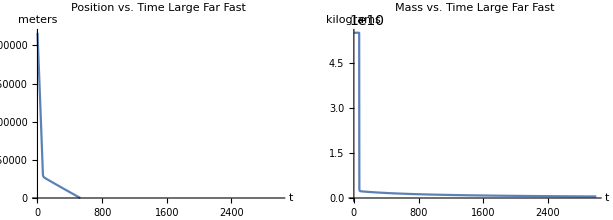

{Impact time with surface,{t→529.945}}

{Resulting Meteor Size,1.50785×10^9}

{Percent of Original Meteor,2.74154 %}

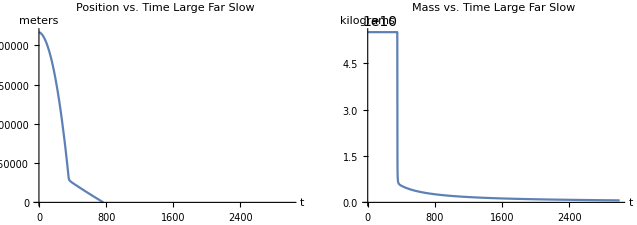

{Impact time with surface,{t→766.865}}

{Resulting Meteor Size,2.73939×10^9}

{Percent of Original Meteor,4.98072 %}

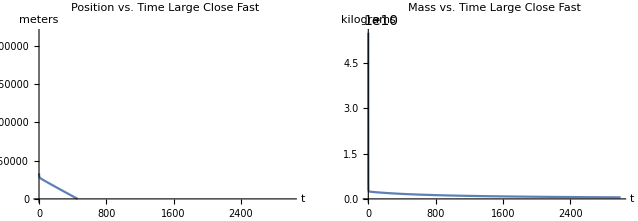

{Impact time with surface,{t→459.235}}

{Resulting Meteor Size,1.58243×10^9}

{Percent of Original Meteor,2.87715 %}

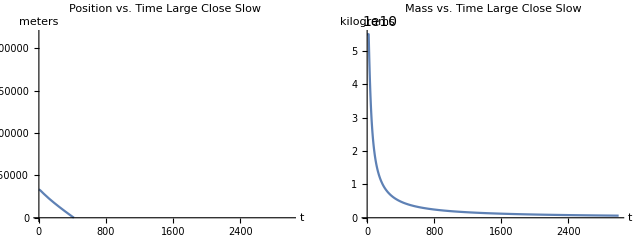

{Impact time with surface,{t→417.448}}

{Resulting Meteor Size,4.66188×10^9}

{Percent of Original Meteor,8.47615 %}

Observing the graphs, because the mass remains unchanged at the larger value while the position and speed are changing between closer and farther distances and faster and slower speeds illustrates their potential effects on the meteor’s position and mass. In terms of the shortest impact time with the surface a slow close meteor wins; however, this meteor has a greater percentage original mass than compared with closer fast and far fast meteor which may seem contradictory. This is because the faster meteors will encounter a lot more drag when entering the atmosphere which slows their descent and deteriorates the mass more rapidly. Additionally, the far fast meteor has a lower percentage original mass than compared with the closer fast meteor because it is able to generate more acceleration and velocity on its long flight time before hitting the atmosphere which causes a slightly higher force of drag as resistance to its velocity in the atmosphere. When the meteor is far and slow it obviously takes the most time to reach the atmosphere and the most time to reach the surface once in the atmosphere. Ultimately, meteors with higher initial speeds will have a reduced impact time and lower percentage original mass. Now, the initial distance away from the Earth shows the greater the distance the meteor starts away from the Earth influences how much momentum the meteor can build up before entering the atmosphere, starting farther away means it will have a longer time until it reaches the atmosphere and a longer time until impact despite its high velocity which the force of drag opposes; its mass will deteriorate a lot faster because the heightened force of atmospheric drag.

## Graphs changing Initial Conditions (SMALL Meteors, far/close Distance, fast/slow meteors)

Let a large meteor be m0=5.5*10^10 and a small be m0=5.5*10^8.
Let a far meteor be s=650000 and a close meteor (just above the atmosphere) be s=100,000.
Let a fast meteor be s’[0]=-9000 and a slow meteor be s’[0]=-100.
Now the graphs will show the effects of the initial conditions given the meteor is of a smaller initial size to cross reference the effects with the previous set of graphs of a large meteor. A smaller mass meteor will not have the same surface area to generate a massive amount of burn from atmospheric drag compared to a relatively larger meteor. In addition, a lower mass meteor means the attractive force of gravity from the Earth will be significantly less, resulting in a lower acceleration towards the Earth while the meteor is above the atmosphere. Also, the force of drag will be less because it depends heavily on the amount of exposed surface area. Moreover, this is likely to result in a longer impact time due to the fact the force of gravity depends more on the mass of the meteor than compared to the drag.

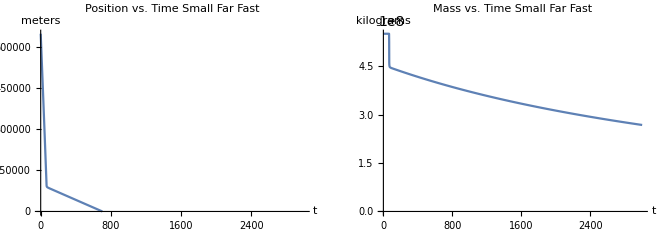

{Impact time with surface,{t→702.911}}

{Resulting Meteor Size,3.92389×10^8}

{Percent of Original Meteor,71.3435 %}

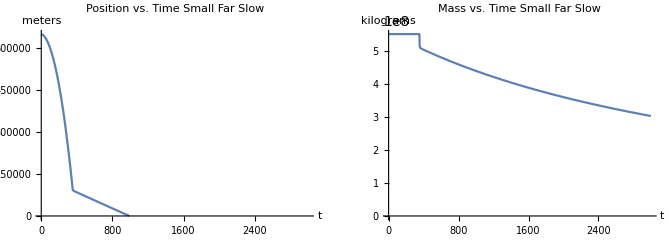

{Impact time with surface,{t→989.963}}

{Resulting Meteor Size,4.39492×10^8}

{Percent of Original Meteor,79.9076 %}

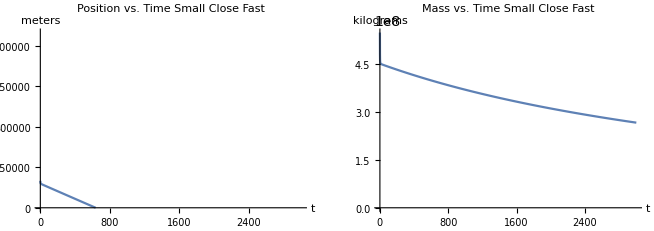

{Impact time with surface,{t→636.132}}

{Resulting Meteor Size,3.96953×10^8}

{Percent of Original Meteor,72.1733 %}

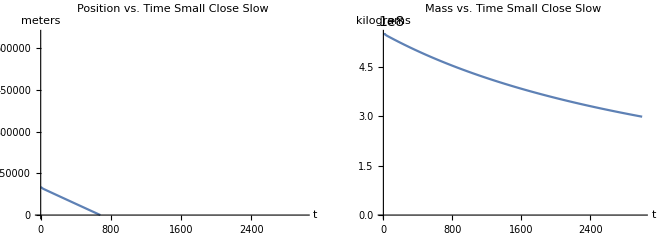

{Impact time with surface,{t→679.605}}

{Resulting Meteor Size,4.66288×10^8}

{Percent of Original Meteor,84.7797 %}

Note the graphs of the smaller mass meteors all have a longer impact time with the surface than compared with those of their respective counterpart larger mass meteors. Additionally, all of the graphs have a higher percentage of original mass than compared to those of larger mass meteors. This mainly can be seen through the fact than while the time in space is a lot shorter than compared with their counterparts on the larger mass meteors, the time in the atmosphere is greater yet the meteors are not deteriorating as much. Ultimately, the meteors have a lower force of gravity and a lower force of atmospheric friction. An explanation for this comes from a lower initial mass will result in a lower proportional decrease in mass. Due to this, the force of drag will remain at lower levels to slow the descent of the meteors. Also because the smaller meteors can not generate nearly enough speed when entering the atmosphere to burn off mass from the force of atmospheric friction because of a lower force of gravity, the change in mass of the meteor will remain at very small values shown by the high percent of original meteor at the impact time.

## Planetary Changes

A big part of the model is that Earth is the assumed planet in question which the meteor is approaching, but when the planet changes the parameters, such as the planet’s radius, mass, atmosphere height, and air density will also change respectively. Looking back at the unit-less equations, the mass of the planet (M), radius of the planet (r), the height of the atmosphere, and the air density (x) play a large role in determining the proportionality of the change in mass of the meteor.  In addition, for the change in position of the meteor, the mass of the planet (M), the radius of the planet (r) influence the force of gravity, while the height of the atmosphere influences the force of drag. 
Obviously, a larger mass planet will increase the force of gravity on a meteor, but the bigger the radius of the planet the wider the planet will be causing a decrease the force of gravity. However, the force of gravity on more massive planets will always be greater than the force of gravity on smaller planets because the radius of the planet only plays a small role in determining the average distance of an object from the planet. Now changes in the height of the meteor will affect when the force of drag occurs, causing the mass to deteriorate and the descent of the meteor to occur (slowing the acceleration and velocity of the meteor). Also, changing the air density (if any) on the planet affects the atmospheric friction which the meteor will experience,  for example a planet such as mercury barely has any atmosphere meaning meteors do not experience the dampening force of atmospheric friction which is one reason why the surface of mercury is so cratered; conversely, if the planet has too density of an atmosphere it will cause the meteor to burn before even reaching the surface of the planet (if any for a gaseous planet). 
For the values of the parameters (assume normal unless otherwise noted),
Mass of the Venus M=4.867*10^24kg, Radius of the Venus r=6.05*10^6, Upper atmosphere height 65000m, air density on Venus 67kg/m^3.
Mass of Jupiter M=1898*10^24kg, Radius of Jupiter r=69.91*10^6,  Upper atmosphere height 1000000m, air density on Jupiter 1326kg/m^3. Because the atmosphere of Jupiter is so much further than Earth’s let the initial position of the meteor be 2000000m away.

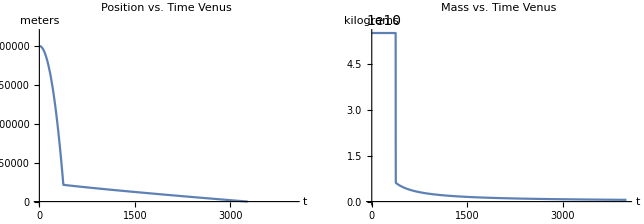

{Impact time with surface,{t→3272.}}

{Resulting Meteor Size,6.96695×10^8}

{Percent of Original Meteor,1.26672 %}

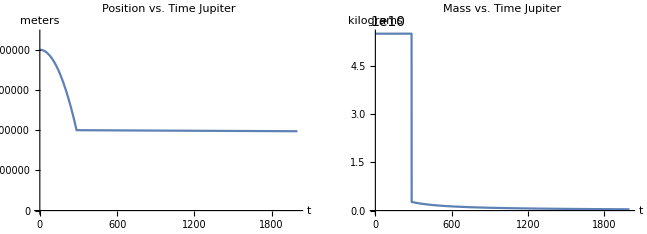

{Impact time with surface,{t→3310.27}}

{Resulting Meteor Size,1.93072×10^8}

{Percent of Original Meteor,0.35104 %}

Observe, Venus is a planet with a very dense atmosphere with a relatively lower atmospheric height than Earth; given this fact, the meteor still deteriorates for a lot longer as the descent takes more time due to the density of the air which results in a greater force of atmospheric friction. Also, the meteor’s percent of original mass is significantly lower than at normal conditions for Earth. Also note the steepness of the position curve (velocity) which shows how much the net force on the meteor is suddenly diminished when entering the atmosphere. Essentially, the resiting force of atmospheric drag is so strong it begins to overpower the force of gravity compared to Earth.
Notice, Jupiter is a very large planet with an incredibly dense atmosphere (and not very much of a surface) also its extensive “atmosphere” which reaches one million meters from its surface. Because of the large mass of the planet, the meteor accelerates very fast due to the force of gravity being so large before crashing into the atmosphere. However, when the meteor enters the atmosphere it almost instantaneously burns up to less than 1% of its original mass. This causes the very fast speed of the meteor in space when entering the atmosphere to drop to closer to zero: like driving a car into a wall. Looking to the graph of the position with such a large time interval, the meteor barely approaches the surface which is due to the extreme decrease in mass: essentially, the mass has burned up so much that Jupiter does not attract it very much anymore. The drag was so great because of the air density that the meteor’s approached was dampened tremendously causing it to rapidly deteriorate. Ultimately, the meteor approaching Jupiter will never reach the “surface” of the planet because it has been destroyed.

## Conclusion

Lastly, the model of the approaching meteor to the surface of a planet should provide the reader with information regarding the affects of many different parameters on the position and mass of a given meteor. Most notably, this provides insight into how important the speed, distance, and size of a meteor are in determining the descent of a meteor. Especially, given a planet with an atmosphere which greatly influences both the approach of a meteor to the surface of the planet and the meteors overall mass. Without an atmosphere the force of atmospheric drag would not exist to hinder and deteriorate a meteor. Also, the force of gravity is a big takeaway in observing the net force of the meteor and how it affects the descent of an object onto the planet’s surface. This model has many extensions beyond just the force of gravity and atmospheric drag and additionally the position and mass of the meteor, such as the force of torque from the spin of the meteor and the temperature of the meteor during its deterioration. Because of many complexities the model forgoes some applications which could be implement for greater understanding: the angle at which the meteor approaches the surface of the planet, the change in atmospheric density from the upper atmosphere to sea level, and the deterioration of the meteor in multiple small pieces instead of a layer by layer burning.